```mathematica
ClearAll["Global`*"]
```

```mathematica
data = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/densitydata.csv"}],"csv"];
```

```mathematica
eqnC = ((λ)/(0.5*(k*(1+MODK))))*R*C-(μ + σ*(1-R/(k*(1+MODK))))*C/.{λ->λ[M],Y->Y[M],μ->μ[M],ρ->ρ[M],σ->σ[M]};(*take σ*(1-R/k)=0 to take out starvation component*)
eqnR = α*(1+MOD)*R*(1-R/(k*(1+MODK)))-(((λ)/(Y))*(R/(0.5*(k*(1+MODK))))+ρ)*C/.{λ->λ[M],Y->Y[M],μ->μ[M],ρ->ρ[M],σ->σ[M]};
LVSS = FullSimplify[Solve[{0==eqnC,0==eqnR},{C,R}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{C→0.,R→0.},{C→0.,R→k (1.+MODK)},{C→(k (1.+MOD) (1.+MODK) α Y[M] (2. λ[M]-1. μ[M]) (μ[M]+σ[M]))/((2. λ[M]+σ[M]) (Y[M] ρ[M] σ[M]+λ[M] (2. μ[M]+2. Y[M] ρ[M]+2. σ[M]))),R→(k (1.+MODK) (μ[M]+σ[M]))/(2. λ[M]+σ[M])}}

```mathematica
Csol = C/.LVSS[[3]]
Rsol = R/.LVSS[[3]]
```

(k (1.+MOD) (1.+MODK) α Y[M] (2. λ[M]-1. μ[M]) (μ[M]+σ[M]))/((2. λ[M]+σ[M]) (Y[M] ρ[M] σ[M]+λ[M] (2. μ[M]+2. Y[M] ρ[M]+2. σ[M])))

(k (1.+MODK) (μ[M]+σ[M]))/(2. λ[M]+σ[M])

```mathematica
jac =FullSimplify[{{ D[eqnR,R],D[eqnR,C]},{D[eqnC,R],D[eqnC,C]}}]/.{C->Csol,R->Rsol}
```

{{1/(k (1.+MODK) Y[M])(α Y[M] (k (1+MOD) (1+MODK)+(k (-2.-2. MOD) (1.+MODK) (μ[M]+σ[M]))/(2. λ[M]+σ[M]))-(2. k (1.+MOD) (1.+MODK) α Y[M] λ[M] (2. λ[M]-1. μ[M]) (μ[M]+σ[M]))/((2. λ[M]+σ[M]) (Y[M] ρ[M] σ[M]+λ[M] (2. μ[M]+2. Y[M] ρ[M]+2. σ[M])))),-ρ[M]-(2. k (1.+MODK) λ[M] (μ[M]+σ[M]))/((k Y[M]+k MODK Y[M]) (2. λ[M]+σ[M]))},{1/(1. k+k MODK)((2. k (1.+MOD) (1.+MODK) α Y[M] λ[M] (2. λ[M]-1. μ[M]) (μ[M]+σ[M]))/((2. λ[M]+σ[M]) (Y[M] ρ[M] σ[M]+λ[M] (2. μ[M]+2. Y[M] ρ[M]+2. σ[M])))+(1. k (1.+MOD) (1.+MODK) α Y[M] (2. λ[M]-1. μ[M]) σ[M] (μ[M]+σ[M]))/((2. λ[M]+σ[M]) (Y[M] ρ[M] σ[M]+λ[M] (2. μ[M]+2. Y[M] ρ[M]+2. σ[M])))),-μ[M]+(2. k (1.+MODK) λ[M] (μ[M]+σ[M]))/((k+k MODK) (2. λ[M]+σ[M]))+σ[M] (-1+(k (1.+MODK) (μ[M]+σ[M]))/((k+k MODK) (2. λ[M]+σ[M])))}}

```mathematica
(* Parameters that go into the model *)
(* Those that rely on mass have been made into functions for better exploration *)

s=1;
B0=4.7*10^(-2);
Em=5774(*J/gram*);
Emprime =7000;
aprime =  B0/Emprime;
η=3/4;
γ=1.19;
ζ=1.00;
f0=0.0202;
mm0=0.383;
α=(*2.10*10^(-9)*)(9.45*10^(-9));
Ed=18200; (*J/g*)
k=(*5*)23000;
(*k=(*10*)23000/2;*)
ρ[M_]:=B0*M^(η)/(M*Ed);
Y[M_]:=M*Ed/BLam[M]; (*g individual/ g grass*)

a0 = 1.88*10^-8 ;(*sec grams^-b0*)
a1=1.45*10^-7;
a2=4.04*10^6;
b0=-0.56;
b1=-0.27;
b2=0.30;
μ[M_] := (a0*(Exp[a1*a2*M^(b1+b2)]-1)*M^(b0-b1-b2))/(a1*a2)   (* this is the consumer death rate*)


B0=4.7*10^(-2);(*W g^−0.75*)
Em=5774;(*J/gram*)
a = B0/Em;
m0[M_]:= (.0558*(1/1000)^.92*M^0.92)*1000;
ϵLam = 0.95;
τLam[M_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0[M]/M)^(1/4))]*(4*M^(1/4))/a;
λ[M_]:=(Log[2]/τLam[M]) (*Fecundity = 2*) (* max consumer growth rate *)

(*STARVATION MORTALITY*)
ϵsig[M_] := (1-(f0*M^γ+mm0*M^ζ)/M);(*mortality from starvation state*)
τsig [M_]:=-M^(1/4)/aprime*Log[ϵsig[M]];(*time it takes to go from full to dead*)
σ[M_] := 1/τsig [M];(*starvation mortality rate)*)

E'=7000; (*J/g*)
a'=B0/E';
m[t_,M_]:=M*E^(-a'*t/(M^(1-η)))


(* Two version of Beta-lambda here. The first one doesn't take long to integrate numerically but gives slightly different results from the analytical version below *)
Bλ[M_]=Integrate[B0*m[t,M]^(η),{t,0,τLam[M]}];

BLam[M_]:=1/(3 a)ⅇ^(-(a τLam[M])/M^(1/4)) M^(1/4) (3 (-1+ⅇ^((a τLam[M])/M^(1/4))) m0[M]+M (-48 ⅇ^((3 a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))-36 ⅇ^((a τLam[M])/(2 M^(1/4))) (-1+(m0[M]/M)^(1/4))^2-16 ⅇ^((a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))^3+3 (-1+4 (m0[M]/M)^(1/4)-6 √(m0[M]/M)+4 (m0[M]/M)^(3/4))+ⅇ^((a τLam[M])/M^(1/4)) (-25+12 (m0[M]/M)^(1/4)+6 √(m0[M]/M)+4 (m0[M]/M)^(3/4)))+3 a ⅇ^((a τLam[M])/M^(1/4)) M^(3/4) τLam[M]);
```

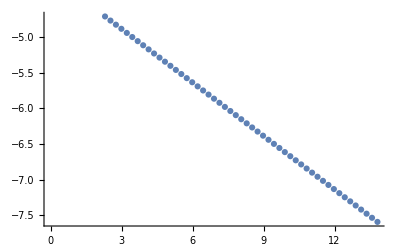

FittedModel[-4.13461-0.250417 x]

```mathematica
datatofit =Table[{Log[10^i],Log[Y[10^i]]},{i,1,6,0.1}];
ListPlot[datatofit]
LinearModelFit[datatofit,x,x]
```

```mathematica
Manipulate[
Max[Re[N[Eigenvalues[jac/.{M->100000,ξ->deathdial}]]]],
{deathdial,0,100}]
```

```mathematica
LM=LinearModelFit[Log@data,x,x]
```

FittedModel[-4.45983-0.776818 x]

```mathematica
Manipulate[
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},PlotRange->{10^-11,10^5}],
LogLogPlot[(1/M)*Csol/.{ξ->deathdial,MOD->mod,MODK->modk},{M,1,1*10^8},Frame->True],
LogLogPlot[Exp[-4.459834805724913]*x^-0.7768181657741381,{x,1,10^8},PlotStyle->Directive[Dashed]]
}],
{deathdial,0,10^-7},
{mod,-1,5},
{modk,-1,10}]
```

{{minmod→-0.970265}}

{{maxmod→1.31746}}

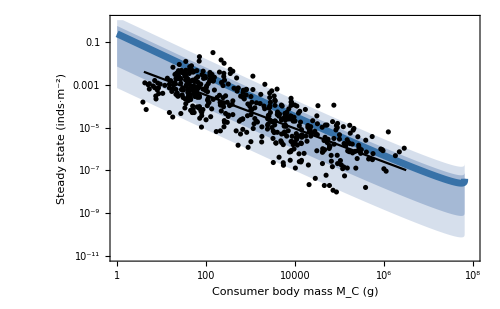

```mathematica
minmodsol = Solve[2.81*10^-10==((9.45*10^(-9))*(1+minmod)),minmod]
maxmodsol=Solve[2.19*10^-8==((9.45*10^(-9))*(1+maxmod)),maxmod]

ConsumerDensityResourcePlot = Show[{
LogLogPlot[
{(1/M)*Csol/.{MOD->0,MODK->0},(1/M)*Csol/.{(MOD->maxmod/.maxmodsol)[[1]],MODK->0},(1/M)*Csol/.{(MOD->minmod/.minmodsol)[[1]],MODK->0},
(1/M)*Csol/.{(MOD->minmod/.minmodsol)[[1]],MODK->-0.9},
(1/M)*Csol/.{(MOD->maxmod/.maxmodsol)[[1]],MODK->1.5}},{M,1,1*10^8},PlotStyle->{ColorData[97,1],Transparent,Transparent,Transparent,Transparent},Filling->{
3->{{2},Directive[ColorData[97,1],Opacity[0.4]]},5->{{4},Directive[ColorData[97,1],Opacity[0.25]]}
},PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Consumer body mass M_C (g)","Steady state (inds·m^-2)"},PlotRange->{10^-11,10^5},LabelStyle->Directive[FontSize->16]],
LogLogPlot[
(1/M)*Csol/.{MOD->0,MODK->0},{M,1,1*10^8},PlotStyle->Directive[ColorData[91,1],Thickness[0.01]]],
ListLogLogPlot[data,PlotStyle->Black],
LogLogPlot[Exp[-4.459834805724913]*x^-0.7768181657741381,{x,4,10^6.5},PlotStyle->Directive[Black]]
},ImageSize->500]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/Figures/fig_consumer2d_resources.pdf"}],ConsumerDensityResourcePlot,"PDF"]
```

/Users/jdyeakel/Dropbox/PostDoc/2021_TaranWebs/Figures/fig_consumer2d_resources.pdf

```mathematica
ColorData[91]
```

ColorDataFunction[…]

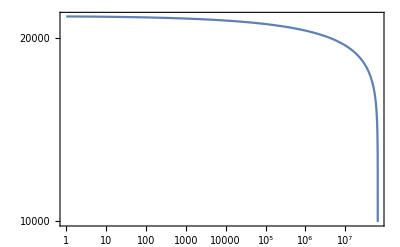

```mathematica
LogLogPlot[Rsol/.{MOD->0},{M,1,1*10^8},Frame->True,PlotRange->{0.01,All}]
```

```mathematica
Remove[maxmod]
```

{{minmod→-0.970265}}

{{maxmod→1.31746}}

5.291*10^10 seconds = 1676 years
2.1164*10^7 seconds = 245 days = 0.67 years

```mathematica
Csol/.M->10
```

(4.05474×10^-13 (1.+MOD))/(1.55451×10^-12+1.30688×10^-8 (7.05843×10^-6 (0.5+0.5 MOD)+2.20234×10^-7 (1.+1. MOD)))

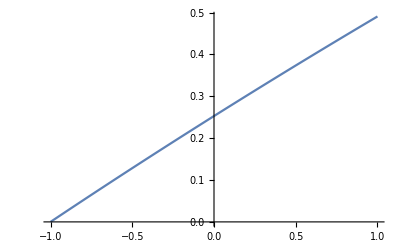

```mathematica
Plot[Csol/.M->10,{MOD,-1,1}]
```

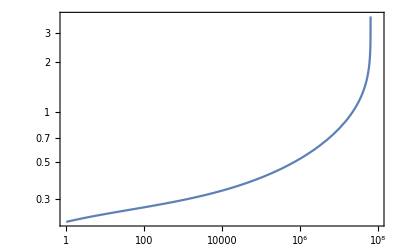

```mathematica
LogLogPlot[Psol/.ξ->0,{M,1,1*10^8},Frame->True]
```

```mathematica
LM=LinearModelFit[Log@data,x,x]
```

FittedModel[-4.45983-0.776818 x]

```mathematica
Exp[LM[x]]
```

ⅇ^(-4.45983-0.776818 x)

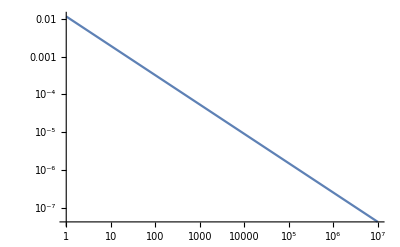

```mathematica
LogLogPlot[Exp[-4.459834805724913]*x^-0.7768181657741381,{x,1,10^7}]
```

```mathematica
Exp[-4.45983]
```

0.0115643

```mathematica
Solve[(k α Y[M] (λ[M]-ξ μ[M]) (ξ μ[M]+σ[M]))/((λ[M]+σ[M]) (Y[M] ρ[M] σ[M]+λ[M] (ξ μ[M]+Y[M] ρ[M]+σ[M])))==0,ξ]
```

{{ξ→λ[M]/μ[M]},{ξ→-σ[M]/μ[M]}}

```mathematica
simdata = Table[{M=10^i,(1/M)*Psol/.{ξ->3.66*^-8,M->10^i}},{i,0,4,0.01}];
```

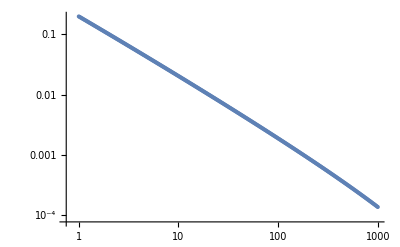

```mathematica
ListLogLogPlot[simdata]
```

```mathematica
model=LinearModelFit[Re[Log10[simdata]],x,x]
```

FittedModel[-0.659776-1.04552 x]

The NSM with external mortality

```mathematica
Manipulate[
LogLogPlot[{(μ[M]+ξ),λ[M],σ[M]},{M,1,10^8}],{ξ,10^-10,10^-8}]
```

```mathematica
Remove[M]
```

```mathematica
critxi = ξ/.Solve[λ[M]==ξ,ξ]
```

{-(1.41054×10^-6)/(M^(1/4) Log[0.0127415/(1.-0.558031/M^0.02)])}

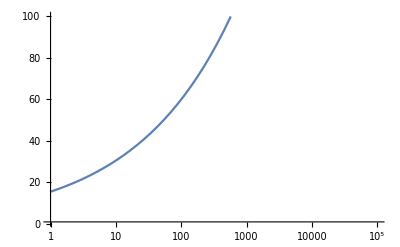

```mathematica
LogLinearPlot[critxi,{M,1,10^5},PlotRange->{1,100}]
```